Пользователей с мощностью сигнала больше единицы: 417

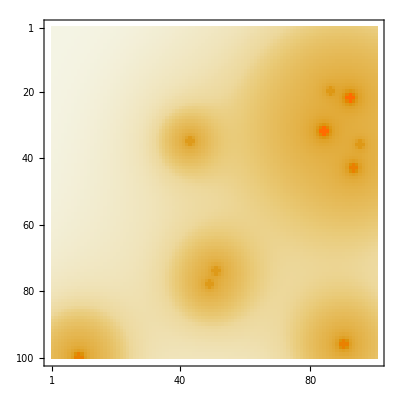

```mathematica
(* 1.2 *)
(* sumPower–переменная, в которую записано поле с мощностью сигнала;coordinates – переменная,хранящая расположение вышек*)
towers={{1,5,100},{2,3,300},{3,2,500}};
Place[towers_]:=Module[{k=1,coordinates={{},{},{}},i,j,position=Table[Table[0,{j,100}],{i,100}]},
For[i=1,i<4,i++,
	For[j=towers[[i,2]],j>0,j--,
	k=1;
	While[k==1,
                    k=0;
		x=RandomInteger[{1,100}];
		y=RandomInteger[{1,100}];
		If[position[[x,y]]==0,AppendTo[coordinates[[i]],{x,y}];position[[x,y]]=i,k=1];
	]
	]
	];
{coordinates,position}
	 ]

{coordinates,position}=Place[towers];
PowerInPoint[coordinates_]:=Module[{i,j,t,k,sumPower={},distance,power},
	For[i=1,i≤100,i++,
		AppendTo[sumPower,{}];
		For[j=1,j≤100,j++,
			power=0;
			For[k=1,k<4,k++,
				For[t=1,t≤towers[[k,2]],t++,
					distance=(i-coordinates[[k,t,1]])^2+(j-coordinates[[k,t,2]])^2;
					If[distance==0,power+=towers[[k,3]],power=power+(towers[[k,3]]/distance)];
					Clear[distance];
				]
			]
	      AppendTo[sumPower[[i]],N[power]];
		]
   ];
	sumPower
	]
sumPower=PowerInPoint[coordinates];
population=Table[Table[0,{j,100}],{i,100}];
For[i=1,i≤100,i++,
	For[j=1,j≤100,j++,
		population[[i,j]]=RandomInteger[{1,100}];
	]
]
users=0;
For[i=1,i≤100,i++,
	For[j=1,j≤100,j++,
		If[N[sumPower[[i,j]]/population[[i,j]]]>1,users++];
               ]
    ]
Print["Количество абонентов, имеющих удовлетворительное качество связи: ",users];
MatrixPlot[sumPower]
```